## Load program

```mathematica
<<"/Users/kouamano/gitsrc/MATH_SCRIPT/SCRIPTS/pointlisttolines.txt"
```

## Execution (picture-edge)

```mathematica
(*file="/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/Carl_F_Gauss.jpg"*)
```

```mathematica
(*file="/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/l_sk_miku.jpg"*)
```

```mathematica
file="/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/about-miku.jpg"
```

/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/about-miku.jpg

```mathematica
(*file="/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/Ofclboxart_cfm_Hatsune_Miku-illu.webp"*)
```

```mathematica
img=Import[file];
```

```mathematica
edgeImage=Thinning[EdgeDetect[ColorConvert[ImagePad[Image[Map[Most,ImageData[img],{2}]],20,White],"Grayscale"]]]
```

-Graphics-

```mathematica
ImageData[edgeImage]
```

{1}
 |  |  |  |

```mathematica
Position[ImageData[edgeImage],1,{2}]
```

{{61,433},{62,426},{62,428},{62,432},{62,434},{63,425},{63,428},{63,431},{63,435},{63,436},{64,424},{64,427},{64,430},29828,{918,708},{918,709},{919,168},{919,170},{919,171},{919,269},{919,272},{919,281},{919,568},{919,597},{920,169},{920,270},{920,271}}
 |  |  |  |

```mathematica
edgePoints={#2,-#1}&@@@Position[ImageData[edgeImage],1,{2}];
```

```mathematica
SeedRandom[2];
hLines=pointListToLines[edgePoints,16];
```

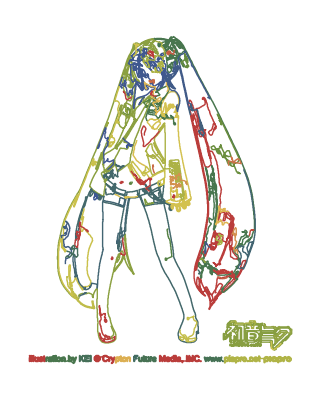

```mathematica
g01=Graphics[{ColorData["DarkRainbow"][RandomReal[]],Line[#]}&/@hLines]
```

```mathematica
Export["/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/HM-g01.jpg",g01]
```

/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/HM-g01.jpg

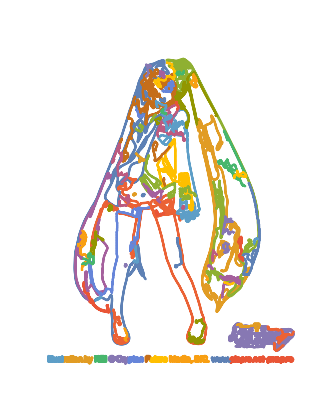

```mathematica
fCs=fourierComponents[hLines];
g02=Show[ParametricPlot[Evaluate[makeFourierSeries[#,t,200]&/@fCs],{t,-Pi,Pi},Axes->False]]
```

```mathematica
Export["/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/HM-g02.jpg",g02]
```

/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/HM-g02.jpg

```mathematica
Partition[Table[paraplot[n],{n,1,200,20}],4]//GraphicsGrid
```

-Graphics-

```mathematica
curves=makeFourierSeries[#,t,200]&/@fCs;
```

```mathematica
Style[Map[Short,Rationalize[curves,0.002]],16]
```

{{«605»+1/14 Sin[199 t]+10/19 Sin[200 t],«1»},{«597»+4/31 Sin[199 t]-5/18 Sin[200 t],-34822/21+«587»},{17814/11+«605»+11/20 Sin[199 t]+11/17 Sin[200 t],«1»},{11922/11+«572»+8/19 Sin[199 t]+17/30 Sin[200 t],-50391/29+«601»+17/52 «1»},{26305/13+(1039 Cos[t])/7+«615»+3/13 Sin[200 t],-39878/15+«587»},{«603»+2/11 Sin[200 t],-14465/29-(2096 «1»)/27+«599»},{«1»,-15764/13+(3186 Cos[t])/7+«574»+7/26 Sin[199 t]-17/35 Sin[200 t]},{50993/39-(1501 Cos[t])/16+«594»+1/22 Sin[199 t]+5/34 Sin[200 t],«1»},{11659/21+(557 Cos[t])/24+«602»,-42750/23-(«1»)/14+«576»},{21217/15-(1363 Cos[t])/15+«586»+1/51 Sin[199 t]-1/98 Sin[200 t],«1»},{22522/11-(5959 Cos[t])/26+«602»+3/26 Sin[200 t],«1»},{6173/8+«598»+1/89 Sin[200 t],-18877/10+«589»+1/9 Sin[200 t]},{11255/8-(2990 Cos[t])/21+«599»+1/13 Sin[199 t]-1/51 Sin[200 t],-(«5»)/9+«592»},{79297/64-(437 Cos[t])/9+«571»+1/21 Sin[199 t]+1/11 Sin[200 t],-(«5»)/23+«638»},{«1»,-35673/32-(2215 Cos[t])/17+«605»+1/167 Sin[199 t]-1/64 Sin[200 t]},{25704/13-(703 Cos[t])/28+«584»+1/15 Sin[199 t]-1/126 Sin[200 t],«1»},{6781/16-(1511 Cos[t])/16+«582»+1/21 Sin[199 t]+1/16 Sin[200 t],«1»},{56317/50-(2326 Cos[t])/17+«597»,-34373/26+«556»+1/111 Sin[200 t]},{18135/23+(817 Cos[t])/35+«587»+1/42 Sin[199 t]+1/169 Sin[200 t],«1»},{10145/13-(2137 Cos[t])/31+«600»+1/77 Sin[199 t]-1/23 Sin[200 t],«1»},{16570/19-(761 Cos[t])/24+«584»+1/26 Sin[198 t]+1/321 Sin[199 t],«1»},{9617/42-(1081 Cos[t])/21+«573»,-185412/65+«590»+1/49 Sin[200 t]},{30884/27-(929 Cos[t])/25+«566»+1/179 Sin[198 t]-1/39 Sin[200 t],«1»},{«536»+1/64 Sin[199 t]+1/74 Sin[200 t],-28129/13+«573»+1/147 Sin[200 t]},{19309/13+(804 Cos[t])/29+«535»+1/101 Sin[198 t]+1/159 Sin[199 t],«1»},{5887/10+«571»+1/208 Sin[199 t]-1/159 Sin[200 t],«540»+1/222 «1»},{65591/70-(1123 Cos[t])/22+«574»,«561»+1/56 Sin[198 t]},{«576»+«1»-1/64 Sin[199 t]-1/47 Sin[200 t],-20483/11+«544»+1/78 Sin[200 t]},{15135/19+«557»+1/69 Sin[199 t]-1/92 Sin[200 t],«1»},{11965/19+(1574 Cos[t])/43+«584»+1/48 Sin[199 t],-54124/19+«577»},{«536»+1/140 Sin[198 t]-1/201 Sin[200 t],-97089/34+«485»+1/140 Sin[200 t]},{28115/18+«555»+1/179 Sin[198 t]-1/163 Sin[199 t],«1»},{36011/26-(139 Cos[t])/8+«521»,«1»},{«565»+«1»+1/59 Sin[199 t]+1/62 Sin[200 t],-36919/14+«564»+1/256 Sin[«1»]},{28035/16+(29 Cos[t])/14+«594»+1/86 Sin[199 t]+1/43 Sin[200 t],-(«5»)/27+«575»},{21654/19-(587 Cos[t])/12+«387»+1/367 Sin[149 t]-1/453 Sin[177 t],«1»},{«610»+1/181 Sin[199 t],-4918/7+(3997 «1»)/37+«538»},{«530»+1/237 Sin[199 t],-3919/11-(1111 «1»)/15+«488»+1/(«3») «1»+1/465 Sin[200 t]},{«569»+1/75 Sin[199 t]+1/201 Sin[200 t],-164993/119+«559»+1/103 Sin[200 t]},{6979/12+(686 Cos[t])/29+«576»+1/115 Sin[199 t]+1/461 Sin[200 t],«1»},{50485/27+«487»+1/420 Sin[194 t]-1/235 Sin[198 t],«532»+1/(«3») «1»},{38383/31+«534»+1/321 Sin[200 t],-5818/13+«498»},{18994/13-(173 Cos[t])/19+«499»+1/244 Sin[199 t],-2375/6+«538»},{17753/21+«411»+1/469 Sin[147 t]-1/444 Sin[159 t],-27529/19+«398»+1/(«3») «1»},{12126/23+«473»,-82807/42+«429»+1/239 Sin[196 t]},{25126/19+«454»,-24984/13+«403»+1/311 Sin[156 t]},{29456/15+«501»+1/337 Sin[180 t]-1/264 Sin[199 t],«472»+1/(«3») «1»},{27433/26-(304 Cos[t])/11+«307»+1/441 Sin[108 t]+1/470 Sin[109 t],«1»},{30759/25-(319 Cos[t])/10+«484»,-19898/13+«481»+1/291 Sin[200 t]},{48667/28+«504»+1/484 Sin[199 t]+1/492 Sin[200 t],-61673/33+«487»+1/(«3») «1»},«1»,{15113/16+«251»+1/458 Sin[69 t]+1/420 Sin[70 t],«1»},{50233/27+«432»+1/456 Sin[195 t],-12221/10+«483»},{36573/31-(332 Cos[t])/35+«352»+1/355 Sin[127 t]+1/369 Sin[137 t],«1»},{12184/17-(106 Cos[t])/27+«340»+1/453 Sin[62 t],-25759/17+«376»+1/449 Sin[«1»]},{28663/25+«488»+1/182 Sin[197 t]-1/192 Sin[199 t],«1»},{49114/49-(892 Cos[t])/21+«219»+1/460 Sin[127 t]+1/488 Sin[128 t],«1»},{«1»,-29050/11+(525 Cos[t])/11+«225»},{17937/11-(755 Cos[t])/54+«282»+1/290 Sin[69 t],«301»+1/467 Sin[«1»]},{31925/24+(655 Cos[t])/31+«179»+1/442 Sin[45 t]-1/325 Sin[47 t],«1»},{«292»+1/458 Sin[108 t]+1/463 Sin[111 t],«1»},{16673/17+«329»,-13997/13-(540 «1»)/19+«324»+1/389 Sin[«1»]+1/406 Sin[135 t]},{55718/57+«282»+1/367 Sin[61 t],-15376/19+«308»+1/482 Sin[81 t]},{41804/19-(1447 Cos[t])/36+«221»+1/365 Sin[19 t]+1/415 Sin[23 t],«1»},{30436/29+«234»+1/452 Sin[97 t]+1/379 Sin[112 t],«1»},{36973/31-(77 Cos[t])/16+«219»+1/434 Sin[90 t]+1/495 Sin[91 t],-(«5»)/18+«248»},{33994/17+(119 Cos[t])/9+«290»+1/470 Sin[165 t]+1/435 Sin[166 t],«1»},{24677/14+(860 Cos[t])/23+«143»,«119»+1/406 Sin[19 t]},{33643/21+(344 Cos[t])/21+«227»+1/280 Sin[25 t]+1/342 Sin[26 t],«1»},{12503/11+(247 Cos[t])/25+«330»+1/492 Sin[191 t],-11891/16+«379»+1/472 Sin[«1»]},{24830/19+«88»,«208»+1/471 Sin[33 t]+1/453 Sin[34 t]},{9747/10-(669 Cos[t])/23+«188»,-14386/21+«273»+1/474 Sin[62 t]},{«173»+1/251 Sin[12 t]+1/349 Sin[16 t],-14960/7+«103»+1/494 Sin[13 t]},{91209/67-(11 Cos[t])/16-77/16 Cos[2 t]+«69»+1/249 Sin[10 t],«1»},{8314/7-(318 Cos[t])/19+«229»+1/271 Sin[23 t]+1/370 Sin[24 t],-(«4»)/15+«223»+«1»},{11076/11-(248 Cos[t])/27+«96»,-35048/25-(15 «1»)/8+«39»+1/470 Sin[11 t]},{28803/31-(125 Cos[t])/28-109/12 «1»+«125»+1/393 Sin[18 t]-1/440 Sin[19 t],«1»},{29561/27-(1819 Cos[t])/130+«339»,«1»},{«137»+1/297 Sin[9 t]+1/485 Sin[12 t],-4514/3+«84»},{«87»+1/439 Sin[12 t],-99090/49-(404 «1»)/47+«159»},{45323/56+«187»+1/499 Sin[43 t],-12007/13+«330»+1/477 Sin[93 t]},{10342/17+«294»+1/461 Sin[171 t]+1/457 Sin[177 t],-34804/15+«230»+1/(«3») «1»}}

## Execution (line-edge)

```mathematica
p01=Plot[Sin[Sin[t]-1],{t,-10,10},Axes->False]
```

-Graphics-

```mathematica
Export["/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/p01.jpg",p01]
```

/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/p01.jpg

```mathematica
(*file="/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/about-miku.jpg"*)
```

```mathematica
(*file="/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/l_sk_miku.jpg"*)
```

```mathematica
file="/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/p01.jpg"
```

/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/p01.jpg

```mathematica
img=Import[file];
```

```mathematica
(*lineImage=ImageLines[img];*)
```

```mathematica
edgeImage=Thinning[EdgeDetect[ColorConvert[ImagePad[Image[Map[Most,ImageData[img],{2}]],20,White],"Grayscale"]]]
```

-Graphics-

```mathematica
edgePoints={#2,-#1}&@@@Position[ImageData[edgeImage],1,{2}]
```

{{119,-31},{120,-31},{227,-31},{228,-31},{229,-31},{336,-31},{337,-31},{117,-32},{118,-32},{121,-32},{226,-32},{230,-32},2897,{264,-233},{265,-233},{266,-233},{267,-233},{268,-233},{297,-233},{298,-233},{299,-233},{300,-233},{301,-233},{373,-233}}
 |  |  |  |

```mathematica
SeedRandom[2];
hLines=pointListToLines[edgePoints,16];
```

```mathematica
Graphics[{ColorData["DarkRainbow"][RandomReal[]],Line[#]}&/@hLines]
```

-Graphics-

```mathematica
fCs=fourierComponents[hLines];
Show[ParametricPlot[Evaluate[makeFourierSeries[#,t,200]&/@fCs],{t,-Pi,Pi},Axes->False]]
```

-Graphics-

```mathematica
Partition[Table[paraplot[n],{n,1,200,20}],4]//GraphicsGrid
```

-Graphics-

```mathematica
curves=makeFourierSeries[#,t,200]&/@fCs;
```

```mathematica
Style[Map[Short,Rationalize[curves,0.002]],16]
```

{{16353/25+«601»+1/120 Sin[200 t],-4991/11+«587»+1/26 Sin[200 t]}}

## Execution (line)

```mathematica
p01=Plot[Sin[Sin[t]-1],{t,-10,10},Axes->False]
```

-Graphics-

```mathematica
Export["/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/p01.jpg",p01]
```

/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/p01.jpg

```mathematica
(*file="/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/about-miku.jpg"*)
```

```mathematica
(*file="/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/l_sk_miku.jpg"*)
```

```mathematica
file="/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/p01.jpg"
```

/Users/kouamano/gitsrc/Kenkyu-kai/Mathematica_Kenkyu-kai/p01.jpg

```mathematica
img=Import[file];
```

```mathematica
lineImage=ImageLines[img];
```

```mathematica
lineImage[[1]]
```

Line[{{0.,111.},{360.,111.}}]

```mathematica
Map[#[[1]]&,lineImage]
```

{{{0.,111.},{360.,111.}},{{0.,216.627},{360.,0.698231}},{{0.,5.37305},{360.,221.302}},{{0.,216.504},{360.,25.909}},{{0.,188.153},{355.387,0.}},{{0.,5.49623},{360.,196.091}},{{0.,33.8472},{355.387,222.}},{{360.,2.10322},{29.4116,222.}},{{360.,219.897},{29.4116,0.}},{{0.,200.992},{360.,16.5031}},{{360.,38.3834},{13.1806,222.}},{{0.,26.6388},{360.,211.128}},{{0.,216.286},{325.159,0.}},{{360.,183.617},{13.1806,0.}},{{0.,145.159},{360.,1.28949}},{{0.,161.348},{360.,17.4792}},{{0.,207.759},{360.,63.8897}},{{0.,182.935},{360.,39.0655}},{{0.,220.711},{360.,76.8415}},{{0.,5.71436},{325.159,222.}},{{0.,14.2413},{360.,158.11}},{{0.,39.0655},{360.,182.935}},{{0.,55.2552},{360.,199.124}},{{0.,193.728},{360.,49.8586}},{{0.,69.2863},{360.,213.155}},{{0.,172.141},{360.,28.2723}},{{0.,28.2723},{360.,172.141}},{{24.6214,222.},{335.379,0.}},{{0.,1.28949},{360.,145.159}},{{330.206,222.},{19.4488,0.}},{{0.,80.0794},{355.124,222.}},{{0.,169.477},{353.644,0.}},{{0.,52.5235},{353.644,222.}},{{360.,217.418},{55.6564,0.}},{{360.,4.58183},{55.6564,222.}},{{0.,153.564},{360.,70.4934}},{{0.,195.736},{360.,112.665}},{{0.,173.107},{360.,90.0364}},{{0.,137.106},{360.,54.0361}},{{0.,126.037},{360.,209.107}},{{0.,212.193},{360.,129.122}},{{0.,40.6646},{360.,123.735}},{{0.,112.665},{360.,195.736}},{{0.,98.2651},{360.,181.335}},{{0.,70.4934},{360.,153.564}},{{0.,54.0361},{360.,137.106}},{{0.,95.9633},{360.,12.8929}},{{0.,137.351},{360.,220.422}},{{0.,123.735},{360.,40.6646}},{{0.,84.8935},{360.,167.964}},{{0.,109.335},{360.,26.2644}},{{0.,29.3502},{360.,112.421}},{{0.,184.421},{360.,101.351}},{{0.,1.5785},{360.,84.6489}},{{0.,122.28},{360.,0.243507}},{{0.,8.27698},{299.171,222.}},{{0.,12.8929},{360.,95.9633}},{{0.,221.756},{360.,99.7203}},{{0.,84.6489},{360.,1.5785}},{{0.,176.44},{360.,62.3819}},{{0.,159.618},{360.,45.5604}},{{0.,99.7203},{360.,221.756}},{{360.,56.969},{15.6324,222.}},{{0.,188.004},{360.,73.9466}},{{360.,140.437},{6.5319,222.}},{{0.,199.569},{360.,85.5114}},{{360.,22.1305},{36.6331,222.}},{{0.,45.5604},{360.,159.618}},{{0.,0.243507},{360.,122.28}},{{0.,62.3819},{360.,176.44}},{{0.,147.227},{360.,30.5217}},{{0.,136.489},{360.,22.4308}},{{360.,165.031},{15.6324,0.}},{{0.,213.723},{299.171,0.}},{{0.,73.9466},{360.,188.004}},{{360.,199.869},{36.6331,0.}},{{0.,22.4308},{360.,136.489}},{{0.,33.9956},{360.,148.053}},{{0.,87.4157},{360.,204.121}},{{0.,197.513},{319.554,0.}},{{0.,24.487},{319.554,222.}},{{0.,150.443},{360.,111.877}},{{0.,168.586},{360.,130.02}},{{0.,166.307},{360.,204.873}},{{0.,177.658},{360.,139.092}},{{0.,139.092},{360.,177.658}},{{0.,204.873},{360.,166.307}},{{0.,130.02},{360.,168.586}},{{0.,195.802},{360.,157.236}},{{0.,159.514},{360.,120.948}},{{0.,157.236},{360.,195.802}},{{0.,179.411},{360.,217.977}},{{0.,159.474},{332.772,0.}},{{0.,91.9798},{360.,53.4138}},{{0.,111.877},{360.,150.443}},{{0.,120.948},{360.,159.514}},{{0.,101.052},{360.,62.4856}},{{0.,62.4856},{360.,101.052}},{{0.,110.123},{360.,71.5574}},{{0.,26.1984},{360.,64.7644}},{{0.,165.391},{360.,77.2463}},{{0.,64.7644},{360.,26.1984}},{{0.,141.371},{360.,102.805}},{{0.,71.5574},{360.,110.123}},{{0.,128.267},{360.,89.701}},{{0.,53.4138},{360.,91.9798}},{{0.,213.945},{360.,175.379}},{{0.,62.526},{332.772,222.}},{{0.,148.164},{360.,186.73}},{{0.,186.73},{360.,148.164}},{{0.,44.342},{360.,82.908}},{{0.,82.908},{360.,44.342}},{{0.,35.2702},{360.,73.8362}},{{0.,221.213},{360.,189.919}},{{0.,73.8362},{360.,35.2702}},{{0.,80.6292},{360.,119.195}},{{0.,93.733},{360.,132.299}},{{0.,214.846},{360.,219.649}},{{0.,102.805},{360.,141.371}},{{0.,119.195},{360.,80.6292}},{{0.,7.15408},{360.,2.35136}},{{0.,158.833},{360.,221.898}},{{360.,115.235},{6.71802,222.}},{{360.,185.072},{51.445,0.}},{{0.,115.235},{353.282,222.}},{{0.,17.1266},{360.,55.6926}},{{360.,106.765},{6.71802,0.}},{{360.,36.9281},{51.445,222.}},{{0.,46.6208},{360.,8.0548}},{{0.,38.0968},{306.607,222.}},{{0.,152.708},{360.,89.6425}},{{360.,206.333},{71.1739,0.}},{{0.,221.898},{360.,158.833}},{{49.9254,222.},{339.741,0.}},{{20.2586,222.},{310.075,0.}},{{0.,55.6926},{360.,17.1266}},{{0.,3.15447},{360.,66.2196}},{{0.,106.765},{353.282,0.}},{{360.,15.6673},{71.1739,222.}},{{0.,4.02289},{360.,42.5889}},{{339.741,222.},{49.9254,0.}},{{0.,66.2196},{360.,3.15447}},{{0.,196.41},{360.,220.458}},{{0.,183.903},{306.607,0.}},{{0.,151.693},{360.,144.488}},{{0.,135.056},{360.,123.045}},{{0.,179.555},{360.,174.753}},{{0.,200.813},{360.,193.608}},{{0.,190.581},{360.,185.778}},{{0.,160.527},{360.,167.732}},{{360.,163.204},{51.7367,0.}},{{0.,123.045},{360.,135.056}},{{0.,76.315},{360.,71.5123}},{{0.,140.264},{360.,137.863}},{{0.,38.8098},{360.,50.8204}},{{0.,88.552},{360.,93.3547}},{{0.,54.2681},{360.,61.4728}},{{0.,31.419},{360.,36.2217}},{{0.,50.8204},{360.,38.8098}},{{305.13,222.},{15.3141,0.}},{{0.,127.235},{360.,112.82}},{{0.,99.5776},{360.,104.38}},{{0.,208.623},{360.,203.82}},{{0.,112.82},{360.,127.235}},{{360.,58.7961},{51.7367,222.}},{{360.,84.0143},{27.657,222.}},{{0.,32.081},{360.,0.786666}},{{0.,21.8259},{280.205,222.}},{{0.,0.0151153},{360.,19.2431}},{{0.,200.174},{280.205,0.}},{{0.,137.986},{332.343,0.}},{{360.,137.986},{27.657,0.}},{{0.,20.3725},{360.,13.1679}},{{87.3553,222.},{357.978,0.}},{{0.,87.2699},{324.502,222.}},{{73.1331,222.},{343.756,0.}},{{2.02193,222.},{272.645,0.}},{{351.657,222.},{81.0343,0.}},{{272.645,222.},{2.02193,0.}},{{310.571,222.},{39.9479,0.}},{{16.2442,222.},{286.867,0.}},{{44.6886,222.},{315.311,0.}},{{360.,27.9845},{88.4156,222.}},{{0.,69.8684},{306.878,222.}},{{360.,194.016},{88.4156,0.}},{{284.97,222.},{63.7095,0.}},{{313.271,222.},{92.01,0.}},{{104.745,222.},{326.006,0.}},{{26.9187,222.},{248.18,0.}},{{128.801,222.},{350.062,0.}},{{12.7684,222.},{234.029,0.}},{{92.01,222.},{313.271,0.}},{{0.0331555,222.},{221.294,0.}},{{299.121,222.},{77.8597,0.}},{{326.006,222.},{104.745,0.}},{{248.18,222.},{26.9187,0.}},{{340.156,222.},{118.896,0.}},{{46.7291,222.},{267.99,0.}},{{0.,172.216},{287.122,0.}},{{231.199,222.},{9.93836,0.}},{{60.8794,222.},{282.14,0.}},{{77.8597,222.},{299.121,0.}},{{360.,120.334},{58.8904,0.}},{{272.235,222.},{50.9742,0.}},{{357.137,222.},{135.876,0.}},{{0.,49.7838},{287.122,222.}},{{0.,152.132},{306.878,0.}},{{0.,101.666},{301.11,222.}},{{360.,217.177},{95.2565,0.}},{{360.,101.666},{58.8904,222.}},{{0.,4.226},{217.049,222.}},{{323.178,222.},{70.2478,0.}},{{0.,120.334},{301.11,0.}},{{360.,4.226},{142.951,222.}},{{360.,147.657},{62.1478,0.}},{{285.194,222.},{32.2645,0.}},{{0.,220.981},{251.769,0.}},{{0.,124.658},{322.101,222.}},{{360.,177.483},{72.852,0.}},{{360.,1.01896},{108.231,222.}},{{67.2092,222.},{320.139,0.}},{{360.,74.343},{62.1478,222.}},{{360.,97.3419},{37.8988,0.}},{{0.,34.1431},{262.964,222.}},{{289.273,222.},{178.295,0.}},{{103.222,222.},{214.2,0.}},{{113.306,222.},{224.284,0.}},{{219.753,222.},{330.731,0.}},{{0.,2.8538},{253.063,222.}},{{20.3047,222.},{131.283,0.}},{{5.73821,222.},{116.716,0.}},{{360.,124.658},{37.8988,222.}},{{196.272,222.},{85.2936,0.}},{{177.223,222.},{66.2451,0.}},{{131.234,222.},{242.212,0.}},{{360.,44.517},{72.852,222.}},{{238.802,222.},{349.78,0.}},{{302.719,222.},{191.741,0.}},{{0.,187.857},{262.964,0.}},{{206.307,222.},{317.285,0.}},{{209.718,222.},{98.7395,0.}},{{317.285,222.},{206.307,0.}},{{0.,207.836},{207.144,0.}},{{0.,97.3419},{322.101,0.}},{{39.8611,222.},{292.791,0.}},{{144.729,222.},{33.7507,0.}},{{182.777,222.},{293.755,0.}},{{159.246,222.},{270.224,0.}},{{42.7146,222.},{153.693,0.}},{{256.778,222.},{145.8,0.}},{{349.78,222.},{238.802,0.}},{{52.7991,222.},{163.777,0.}},{{360.,207.836},{152.856,0.}},{{131.283,222.},{20.3047,0.}},{{145.8,222.},{256.778,0.}},{{339.695,222.},{228.717,0.}},{{270.224,222.},{159.246,0.}},{{121.198,222.},{10.2202,0.}},{{242.212,222.},{131.234,0.}},{{224.284,222.},{113.306,0.}},{{66.2451,222.},{177.223,0.}},{{196.223,222.},{307.201,0.}},{{163.777,222.},{52.7991,0.}},{{85.2936,222.},{196.272,0.}},{{0.,74.6727},{278.275,222.}},{{0.,57.0621},{325.732,0.}},{{360.,57.0621},{34.2679,0.}},{{360.,57.9648},{86.5177,222.}},{{0.,147.327},{278.275,0.}},{{360.,164.035},{86.5177,0.}},{{360.,40.3016},{105.657,222.}},{{0.,144.316},{317.276,222.}},{{360.,181.698},{105.657,0.}},{{0.,21.2631},{200.069,222.}},{{360.,21.2631},{159.931,222.}},{{360.,212.517},{114.592,0.}},{{0.,77.6836},{317.276,0.}},{{360.,6.45283},{252.248,222.}},{{360.,77.6836},{42.7243,0.}},{{360.,215.547},{252.248,0.}},{{0.,6.45283},{107.752,222.}},{{0.,203.736},{241.71,0.}},{{360.,18.2641},{118.29,222.}},{{360.,79.2089},{90.2927,222.}},{{360.,112.459},{85.8978,222.}},{{360.,142.791},{90.2927,0.}},{{0.,18.2641},{241.71,222.}},{{0.,112.459},{274.102,222.}},{{0.,174.308},{243.998,0.}},{{0.,190.799},{190.163,0.}},{{360.,147.412},{55.3671,222.}},{{360.,190.799},{169.837,0.}},{{0.,167.99},{308.307,222.}},{{360.,167.99},{51.6928,222.}},{{0.,109.541},{274.102,0.}},{{0.,57.4776},{266.179,222.}},{{0.,164.522},{266.179,0.}},{{0.,206.581},{103.27,0.}},{{0.,47.692},{243.998,222.}},{{360.,109.541},{85.8978,0.}},{{360.,205.768},{56.0914,222.}},{{360.,51.3871},{121.175,222.}},{{360.,202.311},{129.502,0.}},{{0.,41.1397},{180.258,222.}},{{360.,38.3001},{176.912,222.}},{{0.,88.7312},{264.382,222.}},{{0.,133.269},{264.382,0.}},{{0.,190.291},{228.839,0.}},{{360.,26.7184},{134.495,222.}},{{360.,170.613},{121.175,0.}},{{16.7443,222.},{210.29,0.}},{{0.,131.771},{284.791,222.}},{{149.71,222.},{343.256,0.}},{{101.842,222.},{295.388,0.}},{{360.,131.771},{75.2091,222.}},{{0.,31.7092},{228.839,222.}},{{295.388,222.},{101.842,0.}},{{0.,173.762},{173.183,0.}},{{0.788412,222.},{194.334,0.}},{{258.158,222.},{64.612,0.}},{{28.7112,222.},{222.257,0.}},{{311.344,222.},{117.798,0.}},{{137.743,222.},{331.289,0.}},{{117.798,222.},{311.344,0.}},{{48.6561,222.},{242.202,0.}},{{360.,173.762},{186.817,0.}},{{194.334,222.},{0.788412,0.}},{{360.,65.7253},{107.165,222.}},{{165.666,222.},{359.212,0.}},{{283.421,222.},{89.8755,0.}},{{359.212,222.},{165.666,0.}},{{0.,90.2295},{284.791,0.}},{{335.278,222.},{141.732,0.}},{{210.29,222.},{16.7443,0.}},{{360.,90.2295},{75.2091,0.}},{{270.125,222.},{76.5789,0.}},{{0.,147.673},{246.204,0.}},{{64.612,222.},{258.158,0.}},{{242.202,222.},{48.6561,0.}},{{360.,35.8024},{63.2324,0.}},{{222.257,222.},{28.7112,0.}},{{76.5789,222.},{270.125,0.}},{{0.,74.3266},{246.204,222.}},{{89.8755,222.},{283.421,0.}},{{0.,161.991},{226.756,0.}},{{323.311,222.},{129.765,0.}},{{347.245,222.},{153.699,0.}},{{360.,156.275},{107.165,0.}},{{360.,123.252},{112.905,222.}},{{360.,96.979},{99.1206,222.}},{{0.,44.5163},{287.897,0.}},{{0.,98.748},{247.095,0.}},{{0.,60.0091},{226.756,222.}},{{0.,123.252},{247.095,222.}},{{0.,183.922},{283.743,222.}},{{0.,58.1767},{163.278,222.}},{{360.,188.653},{142.15,0.}},{{0.,153.603},{279.347,222.}},{{360.,98.748},{112.905,0.}},{{0.,68.397},{279.347,0.}},{{360.,128.779},{104.524,0.}},{{360.,58.1767},{196.722,222.}},{{0.,37.0246},{210.747,222.}},{{360.,221.368},{182.081,0.}},{{0.,184.975},{210.747,0.}},{{175.196,222.},{1.59164,0.}},{{360.,63.7043},{138.416,222.}},{{360.,80.1702},{123.539,222.}},{{184.804,222.},{358.408,0.}},{{360.,37.0246},{149.253,222.}},{{360.,68.397},{80.6528,0.}},{{360.,158.296},{138.416,0.}},{{0.,126.915},{239.719,0.}},{{101.734,222.},{268.289,0.}},{{268.289,222.},{101.734,0.}},{{360.,141.83},{123.539,0.}},{{134.597,222.},{303.478,0.}},{{56.5218,222.},{225.403,0.}},{{1.59164,222.},{175.196,0.}},{{0.,156.724},{156.203,0.}},{{307.256,222.},{138.375,0.}},{{341.257,222.},{172.376,0.}},{{0.,95.0854},{239.719,222.}},{{172.376,222.},{341.257,0.}},{{235.477,222.},{66.596,0.}},{{253.254,222.},{86.6989,0.}},{{196.439,222.},{27.5583,0.}},{{293.404,222.},{124.523,0.}},{{360.,156.724},{203.797,0.}},{{18.7433,222.},{187.624,0.}},{{32.5954,222.},{201.476,0.}},{{119.486,222.},{288.367,0.}},{{71.6332,222.},{240.514,0.}},{{185.106,222.},{16.2247,0.}},{{147.19,222.},{316.071,0.}},{{207.773,222.},{38.8918,0.}},{{43.9289,222.},{212.81,0.}},{{280.811,222.},{111.93,0.}},{{158.524,222.},{327.405,0.}},{{322.367,222.},{153.487,0.}},{{222.23,222.},{57.9781,0.}},{{85.4853,222.},{254.366,0.}},{{202.658,222.},{357.92,0.}},{{360.,156.699},{93.2956,222.}},{{360.,219.479},{197.613,0.}},{{159.849,222.},{0.134964,0.}},{{0.134964,222.},{159.849,0.}},{{360.,180.526},{91.7795,222.}},{{343.244,222.},{187.982,0.}},{{94.6886,222.},{241.29,0.}},{{316.957,222.},{170.355,0.}},{{193.698,222.},{342.436,0.}},{{19.977,222.},{168.715,0.}},{{175.232,222.},{28.6305,0.}},{{360.,75.2138},{213.703,222.}},{{0.,21.8755},{272.721,0.}},{{0.,80.7674},{254.926,0.}},{{360.,141.233},{105.074,222.}},{{203.214,222.},{58.7293,0.}},{{0.,141.233},{254.926,222.}},{{34.6358,222.},{181.237,0.}},{{301.343,222.},{154.741,0.}},{{58.6569,222.},{205.259,0.}},{{0.,75.2138},{146.297,222.}},{{160.747,222.},{307.348,0.}},{{0.,148.442},{207.79,0.}},{{70.6675,222.},{217.269,0.}},{{178.763,222.},{325.364,0.}},{{142.731,222.},{289.333,0.}},{{0.,73.558},{207.79,222.}},{{283.327,222.},{136.726,0.}},{{360.,175.147},{154.998,0.}},{{360.,50.1553},{94.577,0.}},{{192.047,222.},{45.4453,0.}},{{45.4453,222.},{192.047,0.}},{{268.915,222.},{122.313,0.}},{{0.,44.5573},{88.7038,222.}},{{0.,177.443},{88.7038,0.}},{{226.878,222.},{80.2759,0.}},{{122.313,222.},{268.915,0.}},{{360.,221.705},{213.593,0.}},{{213.091,222.},{70.7056,0.}},{{0.,139.779},{226.148,0.}},{{360.,97.0222},{134.947,222.}},{{246.263,222.},{101.779,0.}},{{0.,221.342},{139.889,0.}},{{81.477,222.},{228.079,0.}},{{360.,124.978},{134.947,0.}},{{360.,80.7674},{105.074,0.}},{{144.619,222.},{0.134317,0.}},{{0.,171.417},{197.947,0.}},{{346.447,222.},{204.061,0.}},{{0.,49.0265},{197.073,222.}},{{0.,82.2206},{226.148,222.}},{{218.321,222.},{356.562,0.}},{{107.758,222.},{252.242,0.}},{{257.026,222.},{112.541,0.}},{{360.,44.5573},{271.296,222.}},{{318.27,222.},{188.116,0.}},{{360.,50.583},{162.053,222.}},{{0.,134.045},{220.087,222.}},{{208.944,222.},{343.109,0.}},{{0.,56.8772},{246.487,0.}},{{157.028,222.},{18.7867,0.}},{{0.,199.537},{167.053,0.}},{{360.,76.0215},{155.658,222.}},{{12.8833,222.},{151.124,0.}},{{0.,20.5449},{166.387,222.}},{{360.,177.443},{271.296,0.}},{{360.,199.192},{190.963,0.}},{{360.,18.2304},{196.225,222.}},{{0.,139.687},{139.222,0.}},{{360.,134.045},{139.913,222.}},{{360.,144.747},{157.382,0.}},{{360.,221.839},{229.94,0.}},{{360.,87.9549},{139.913,0.}},{{0.,0.160662},{130.06,222.}},{{360.,139.687},{220.778,0.}},{{0.,87.9549},{220.087,0.}},{{0.,215.894},{126.574,0.}},{{0.,107.56},{216.157,222.}},{{166.112,222.},{290.366,0.}},{{360.,166.306},{170.524,0.}},{{0.,111.861},{225.644,0.}},{{360.,2.1423},{231.102,222.}},{{0.,181.335},{360.,98.2651}},{{0.,167.964},{360.,84.8935}},{{0.,21.1215},{360.,104.192}},{{0.,148.053},{360.,33.9956}},{{0.,85.5114},{360.,199.569}},{{0.,0.810152},{360.,104.385}},{{0.,132.299},{360.,93.733}},{{0.,27.7175},{360.,115.862}},{{0.,219.649},{360.,214.846}},{{0.,40.8022},{360.,103.867}},{{0.,15.8943},{360.,91.4113}},{{0.,199.583},{360.,221.22}},{{0.,184.773},{360.,177.569}},{{0.,168.547},{360.,175.751}},{{0.,75.9135},{360.,87.924}},{{0.,69.4923},{360.,62.2877}},{{0.,87.924},{360.,75.9135}},{{0.,164.348},{360.,149.933}},{{0.,149.933},{360.,164.348}},{{0.,36.2217},{360.,31.419}},{{0.,122.422},{360.,117.62}},{{0.,49.8407},{360.,61.8512}},{{0.,62.854},{360.,50.8435}},{{111.82,222.},{333.081,0.}},{{17.0135,222.},{238.274,0.}},{{292.045,222.},{70.7846,0.}},{{275.065,222.},{53.8043,0.}},{{29.7488,222.},{251.01,0.}},{{360.,116.382},{38.0167,0.}},{{0.,1.01896},{251.769,222.}},{{215.271,222.},{326.249,0.}},{{293.755,222.},{182.777,0.}},{{24.7867,222.},{135.765,0.}},{{10.2202,222.},{121.198,0.}},{{205.236,222.},{94.2576,0.}},{{228.717,222.},{339.695,0.}},{{307.201,222.},{196.223,0.}},{{262.33,222.},{41.069,0.}},{{70.7271,222.},{181.705,0.}},{{335.213,222.},{224.235,0.}},{{228.766,222.},{117.788,0.}},{{178.295,222.},{289.273,0.}},{{191.741,222.},{302.719,0.}},{{191.79,222.},{80.8116,0.}},{{0.,215.547},{107.752,0.}},{{360.,128.701},{66.7322,0.}},{{0.,208.979},{238.095,0.}},{{360.,112.779},{77.7956,0.}},{{360.,31.7092},{131.161,222.}},{{52.6451,222.},{246.191,0.}},{{202.312,222.},{8.76636,0.}},{{0.,185.059},{289.931,222.}},{{40.6781,222.},{234.224,0.}},{{186.66,222.},{0.800258,0.}},{{218.682,222.},{107.704,0.}},{{360.,93.2207},{104.524,222.}},{{360.,185.385},{140.062,0.}},{{303.478,222.},{134.597,0.}},{{163.561,222.},{332.442,0.}},{{284.589,222.},{115.708,0.}},{{174.894,222.},{343.775,0.}},{{80.4482,222.},{249.329,0.}},{{317.33,222.},{148.449,0.}},{{166.8,222.},{0.245081,0.}},{{69.1146,222.},{237.996,0.}},{{177.863,222.},{15.8906,0.}},{{328.664,222.},{159.783,0.}},{{360.,200.125},{87.2788,222.}},{{0.,17.0053},{176.327,222.}},{{149.412,222.},{0.674647,0.}},{{52.6516,222.},{199.253,0.}},{{199.253,222.},{52.6516,0.}},{{289.333,222.},{142.731,0.}},{{186.042,222.},{39.44,0.}},{{209.519,222.},{67.1336,0.}},{{161.36,222.},{16.8757,0.}},{{112.541,222.},{257.026,0.}},{{171.901,222.},{31.5963,0.}},{{16.4253,222.},{154.666,0.}},{{360.,145.979},{155.658,0.}},{{133.545,222.},{3.39118,0.}},{{0.,18.7582},{156.762,222.}},{{198.082,222.},{326.254,0.}},{{290.363,222.},{168.047,0.}},{{0.,111.341},{227.013,222.}},{{335.379,222.},{24.6214,0.}},{{0.,104.437},{360.,187.507}},{{0.,217.336},{360.,134.265}},{{0.,90.0364},{360.,173.107}},{{0.,115.506},{360.,32.4359}},{{0.,26.2644},{360.,109.335}},{{0.,114.722},{360.,197.793}},{{0.,125.792},{360.,42.7217}},{{0.,206.021},{360.,122.951}},{{0.,112.238},{360.,16.4195}},{{0.,54.26},{316.831,222.}},{{0.,77.2463},{360.,165.391}},{{0.,218.846},{360.,155.78}},{{0.,99.2791},{360.,28.7622}},{{0.,8.0548},{360.,46.6208}},{{0.,89.6425},{360.,152.708}},{{310.075,222.},{20.2586,0.}},{{0.,0.786666},{360.,32.081}},{{0.,144.488},{360.,151.693}},{{0.,171.18},{360.,183.19}},{{0.,183.19},{360.,171.18}},{{0.,185.588},{360.,192.793}},{{0.,128.645},{360.,133.448}},{{0.,208.832},{360.,201.627}},{{0.,78.3268},{360.,85.5314}},{{0.,47.2474},{360.,42.4447}},{{0.,40.7924},{360.,28.7818}},{{0.,28.7818},{360.,40.7924}},{{0.,117.62},{360.,122.422}},{{0.,27.3812},{292.586,222.}},{{0.,32.9485},{360.,18.5335}},{{0.,18.5335},{360.,32.9485}},{{315.311,222.},{44.6886,0.}},{{286.867,222.},{16.2442,0.}},{{0.,31.6796},{266.412,222.}},{{360.,141.221},{30.0814,222.}},{{292.791,222.},{39.8611,0.}},{{0.,53.2899},{281.276,222.}},{{117.788,222.},{228.766,0.}},{{98.7395,222.},{209.718,0.}},{{200.754,222.},{89.7756,0.}},{{149.211,222.},{38.2327,0.}},{{274.706,222.},{163.728,0.}},{{358.744,222.},{247.766,0.}},{{330.731,222.},{219.753,0.}},{{237.73,222.},{126.752,0.}},{{38.2327,222.},{149.211,0.}},{{57.2811,222.},{168.259,0.}},{{360.,164.938},{34.2679,222.}},{{360.,122.308},{45.344,222.}},{{214.2,222.},{103.222,0.}},{{360.,204.764},{37.2999,222.}},{{360.,17.2358},{37.2999,0.}},{{0.,43.9968},{249.17,222.}},{{0.,61.0123},{260.46,222.}},{{360.,150.507},{68.01,222.}},{{24.7222,222.},{218.268,0.}},{{36.6892,222.},{230.235,0.}},{{12.7553,222.},{206.301,0.}},{{0.,57.5457},{230.204,222.}},{{360.,197.616},{261.212,0.}},{{360.,177.484},{72.1032,222.}},{{360.,44.5163},{72.1032,0.}},{{345.298,222.},{234.32,0.}},{{263.277,222.},{96.7225,0.}},{{187.624,222.},{18.7433,0.}},{{275.774,222.},{106.893,0.}},{{289.626,222.},{120.745,0.}},{{201.476,222.},{32.5954,0.}},{{253.107,222.},{84.226,0.}},{{154.746,222.},{323.627,0.}},{{212.81,222.},{43.9289,0.}},{{0.,69.8629},{212.963,222.}},{{313.354,222.},{166.752,0.}},{{241.29,222.},{94.6886,0.}},{{325.364,222.},{178.763,0.}},{{265.311,222.},{118.71,0.}},{{274.963,222.},{130.478,0.}},{{250.152,222.},{109.848,0.}},{{360.,165.123},{113.513,222.}},{{217.74,222.},{358.044,0.}},{{360.,56.8772},{113.513,0.}},{{14.0639,222.},{152.305,0.}},{{327.885,222.},{193.72,0.}},{{195.386,222.},{73.0701,0.}}}

```mathematica
edgeImage=Thinning[EdgeDetect[ColorConvert[ImagePad[Image[Map[Most,ImageData[img],{2}]],20,White],"Grayscale"]]]
```

-Graphics-

```mathematica
ImageData[edgeImage]
```

{1}
 |  |  |  |

```mathematica
Position[ImageData[edgeImage],1,{2}]
```

{{31,119},{31,120},{31,227},{31,228},{31,229},{31,336},{31,337},{32,117},{32,118},{32,121},{32,226},{32,230},{32,334},2894,{233,191},{233,192},{233,264},{233,265},{233,266},{233,267},{233,268},{233,297},{233,298},{233,299},{233,300},{233,301},{233,373}}
 |  |  |  |

```mathematica
edgePoints={#2,-#1}&@@@Position[ImageData[edgeImage],1,{2}]
```

{{119,-31},{120,-31},{227,-31},{228,-31},{229,-31},{336,-31},{337,-31},{117,-32},{118,-32},{121,-32},{226,-32},{230,-32},2897,{264,-233},{265,-233},{266,-233},{267,-233},{268,-233},{297,-233},{298,-233},{299,-233},{300,-233},{301,-233},{373,-233}}
 |  |  |  |

```mathematica
SeedRandom[2];
hLines=pointListToLines[edgePoints,16];
```

```mathematica
Graphics[{ColorData["DarkRainbow"][RandomReal[]],Line[#]}&/@hLines]
```

-Graphics-

```mathematica
fCs=fourierComponents[hLines];
Show[ParametricPlot[Evaluate[makeFourierSeries[#,t,200]&/@fCs],{t,-Pi,Pi},Axes->False]]
```

-Graphics-

```mathematica
Partition[Table[paraplot[n],{n,1,200,20}],4]//GraphicsGrid
```

-Graphics-

```mathematica
curves=makeFourierSeries[#,t,200]&/@fCs;
```

```mathematica
Style[Map[Short,Rationalize[curves,0.002]],16]
```

{{16353/25+«601»+1/120 Sin[200 t],-4991/11+«587»+1/26 Sin[200 t]}}